```mathematica
{{{{hex[x_,y_]:={Line[{p[x,y]+{-(√3)/2,-1/2},p[x,y]+{-(√3)/2,1/2},p[x,y]+{0,1},p[x,y]+{(√3)/2,1/2},p[x,y]+{(√3)/2,-1/2},p[x,y]+{0,-1},p[x,y]+{-(√3)/2,-1/2}}]}}}}}
```

```mathematica
hex[x_,y_,c_]:={Hue[c,1/2],Polygon[{p[x,y]+{-(√3)/2,-1/2},p[x,y]+{-(√3)/2,1/2},p[x,y]+{0,1},p[x,y]+{(√3)/2,1/2},p[x,y]+{(√3)/2,-1/2},p[x,y]+{0,-1},p[x,y]+{-(√3)/2,-1/2}}]}
```

```mathematica
h[x_,y_,1]:={c=Random[];,hex[x,y,c],hex[x+1,y,c],hex[x+2,y+1,c],hex[x+3,y+2,c],hex[x,y+1,c],hex[x,y+2,c]}
```

```mathematica
h[x_,y_,2]:={c=Random[];,hex[x,y,c],hex[x+1,y,c],hex[x+2,y,c],hex[x+3,y+1,c],hex[x+3,y+2,c],hex[x+3,y+3,c]}
```

```mathematica
h[x_,y_,3]:={c=Random[];,hex[x,y,c],hex[x+1,y+1,c],hex[x+2,y+2,c],hex[x+2,y+3,c],hex[x+1,y+3,c],hex[x,y+3,c]}
```

```mathematica
h[x_,y_,4]:={c=Random[];,hex[x,y,c],hex[x+1,y+1,c],hex[x+2,y+2,c],hex[x+3,y+2,c],hex[x+3,y+1,c],hex[x+3,y,c]}
```

```mathematica
h[x_,y_,5]:={c=Random[];,hex[x,y,c],hex[x,y+1,c],hex[x,y+2,c],hex[x+1,y+3,c],hex[x+2,y+3,c],hex[x+3,y+3,c]}
```

```mathematica
h[x_,y_,6]:={c=Random[];,hex[x,y,c],hex[x+1,y,c],hex[x+2,y,c],hex[x,y+1,c],hex[x+1,y+2,c],hex[x+2,y+3,c]}
```

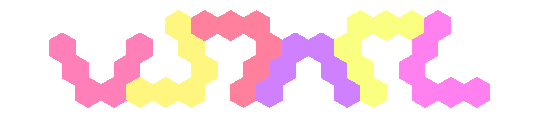

```mathematica
Graphics[{h[0,0,1],h[2,0,2],h[6,0,3],h[7,0,4],h[11,0,5],h[13,0,6]}]
```

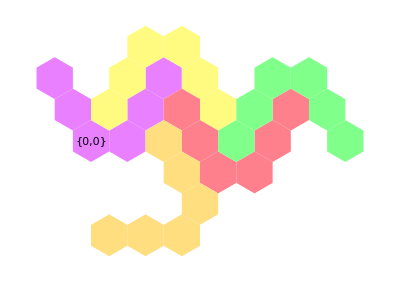

```mathematica
Graphics[{h[0,0,1],Black,Text["{0,0}",{0,0}],h[1,1,4],h[3,-1,1],h[4,0,4],h[-1,-3,2]}]
```

```mathematica
Clear[t]
```

```mathematica
t[x_,y_,1]:={Hue[0,1/2],Map[Rectangle[{x,y}+#]&,{{0,1},{0,0},{1,0},{2,0},{3,0},{4,0},{4,1}}]};
```

```mathematica
t[x_,y_,2,c_:Random[]]:={Hue[1/4,1/2],Map[Rectangle[{x,y}+#]&,{{0,0},{1,0},{1,1},{1,2},{1,3},{1,4},{0,4}}]};
```

```mathematica
t[x_,y_,3]:={Hue[1/2,1/2],Map[Rectangle[{x,y}+#]&,{{0,0},{0,1},{1,1},{2,1},{3,1},{4,1},{4,0}}]};
```

```mathematica
t[x_,y_,4]:={Hue[3/4,1/2],Map[Rectangle[{x,y}+#]&,{{1,0},{0,0},{0,1},{0,2},{0,3},{0,4},{1,4}}]};
```

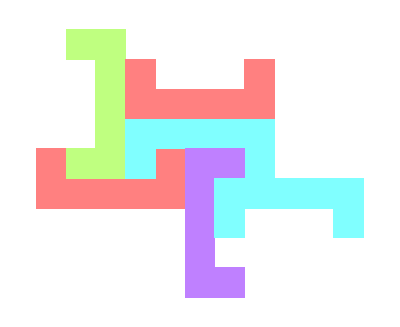

```mathematica
Graphics[{t[0,0,1],t[1,1,2],t[3,1,3],t[5,-3,4],t[6,-1,3],t[3,3,1]}]
```